## Construction of the NxN matrix

```mathematica
Quit[]
```

```mathematica
Clear[m,k,M]
```

```mathematica
(*definition of the parameters*)
m=125
k=500
M=5000
N[k^4/M^2]
N[k^2/M^2]
N[m^2/M^2]
```

125

500

5000

2500.

0.01

0.000625

```mathematica
n=10
```

10

```mathematica
(*Creates a n matrices of each of them with dimension ixi with M^2 on the diagonal, k^2 on the first row and first column and m^2 on the first entry*)
AnalyticMass={} ;(*Factor=0.01, number of higgs=10*)
Entry[i_,j_]:=0
For[i=1,i<n+1,i++,
Entry[1,i]=k^2;
Entry[i,1]=k^2;
If[i==1,Entry[1,1]=m^2,Entry[i,i]=M^2];
MassMatrix=Array[Entry,{i,i}];
Print[Eigenvalues[MassMatrix]]
(*
Useful to know the analytic eigenvalues, but only gives as the minimum if we put already numerical values and we are we loose sense of the position of the eigenvalues in the matrix, therefore, better calculating the eigenvalues via rotation;*);
Lista=N[Eigenvalues[MassMatrix]];
AppendTo[AnalyticMass,{i,Lista[[i-1]]}];
]
```

{m^2}

{1/2 (m^2+M^2-√(4 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(4 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,1/2 (m^2+M^2-√(8 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(8 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,1/2 (m^2+M^2-√(12 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(12 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,M^2,1/2 (m^2+M^2-√(16 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(16 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,M^2,M^2,1/2 (m^2+M^2-√(20 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(20 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,M^2,M^2,M^2,1/2 (m^2+M^2-√(24 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(24 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,M^2,M^2,M^2,M^2,1/2 (m^2+M^2-√(28 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(28 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,M^2,M^2,M^2,M^2,M^2,1/2 (m^2+M^2-√(32 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(32 k^4+m^4-2 m^2 M^2+M^4))}

{M^2,M^2,M^2,M^2,M^2,M^2,M^2,M^2,1/2 (m^2+M^2-√(36 k^4+m^4-2 m^2 M^2+M^4)),1/2 (m^2+M^2+√(36 k^4+m^4-2 m^2 M^2+M^4))}

```mathematica
(*For the more general rotation use this matrix:
AnalyticMass={} 
For[i=1,i<n+1,i++,
(*Print[i];*)
For[a=1,a<=i,a++,If[a==(j+1),Entry[j+1,a]=M^2,Entry[j+1,a]=k ^2]];
For[a=1,a<=i,a++,If[a==(j+1),Entry[a,j+1]=M^2,Entry[a,j+1]=k ^2]];
Clear[j];
Entry[1,1]=m^2;
MassMatrix=Array[Entry,{i,i}];
Lista=N[Eigenvalues[MassMatrix]];
Print[Lista];
AppendTo[AnalyticMass,{i,Lista[[i]]}];
j=i
]

*)
```

```mathematica
MassMatrix //MatrixForm
```

(m^2 | k^2 | k^2 | k^2 | k^2 | k^2 | k^2 | k^2 | k^2 | k^2
k^2 | M^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
k^2 | 0 | M^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
k^2 | 0 | 0 | M^2 | 0 | 0 | 0 | 0 | 0 | 0
k^2 | 0 | 0 | 0 | M^2 | 0 | 0 | 0 | 0 | 0
k^2 | 0 | 0 | 0 | 0 | M^2 | 0 | 0 | 0 | 0
k^2 | 0 | 0 | 0 | 0 | 0 | M^2 | 0 | 0 | 0
k^2 | 0 | 0 | 0 | 0 | 0 | 0 | M^2 | 0 | 0
k^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | M^2 | 0
k^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | M^2)

## Rotating/Diagonalizing the matrix

```mathematica
(*Definition of the coupling with the w-bosons, formula dependent on n, dimension of the matrix*)
Coupling[i_]:=Product[Cos[θ[r]],{r,1,i-1}]
```

```mathematica
(* In this For we do each rotation, i.e. we calculate the angle relative to every rotation and how will change the first entry of the matrix after each rotation*)
(*We get as a result the each rotation angle, and the eigenvalue we find after this rotation*)
MassMatrix[[1,1]]=m^2;
EigenvaluesRotation={};
For[i=1,i<n,i++,
θ[i]=N[1/2 ArcTan[2MassMatrix[[1,i+1]]/(-MassMatrix[[1,1]]+MassMatrix[[i+1,i+1]])]];
AppendTo[EigenvaluesRotation,{i+1,Cos[θ[i]]^2 MassMatrix[[1,1]]-2 Cos[θ[i]] k^2 Sin[θ[i]]+M^2 Sin[θ[i]]^2}];
MassMatrix[[1,1]]=Cos[θ[i]]^2 MassMatrix[[1,1]]- Cos[θ[i]] MassMatrix[[1,i+1]] Sin[θ[i]]- Cos[θ[i]] MassMatrix[[i+1,1]] Sin[θ[i]]+MassMatrix[[i+1,i+1]] Sin[θ[i]]^2;]
(*In the following list we anotate the kawa coupling of each value*)
NvsCoupling={};
For[i=1,i<n,i++,AppendTo[NvsCoupling, {i,Coupling[i]}]]
```

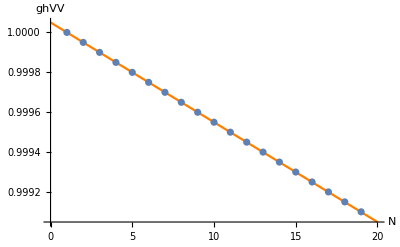

```mathematica
Show[Plot[1-(x-1)/2k^4/M^4,{x,0,20}, PlotStyle->Orange],ListPlot[NvsCoupling],AxesLabel->{Style["N",14],Style[ghVV,14]}]
```

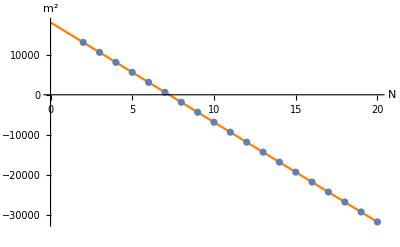

```mathematica
Show[Plot[m^2-(x-1)k^4/M^2,{x,0,20},PlotStyle->Orange], ListPlot[EigenvaluesRotation],AxesLabel->{Style["N",14],Style["m"^2,14]}]
```

```mathematica
(*Prove that the eigenvalues are the same, calculated analytically of by rotations*)
EigenvaluesRotation
AnalyticMass
ListPlot[{EigenvaluesRotation,AnalyticMass},  PlotLegends->Placed[{"Rotation","Analytic"},{1,0.5}]]
```

-Graphics-

#### Relative error

```mathematica
massFormula[x_]:=m^2-(x-1)k^4/M^2
gFormula[x_]:=1-(x-1)/2k^4/M^4
```

```mathematica
EigenvaluesRotation[[1,2]]
```

15606.9

```mathematica
gRelativeError={}
mRelativeError={}
For[i=2,i<=n,i++,
AppendTo[gRelativeError,{i,Abs[gFormula[i]-NvsCoupling[[i-1,2]]]/gFormula[i]}];
AppendTo[mRelativeError, {i, Abs[massFormula[i]-EigenvaluesRotation[[i-1,2]]]/massFormula[i]}]
]
```

{}

{}

```mathematica
ListPlot[{mRelativeError25,mRelativeError50,mRelativeError60,mRelativeError70, mRelativeError75,mRelativeError80,mRelativeError90,mRelativeError100},PlotLegends->Placed[{"k=25, r=0.0025, f=1.56","k=50, r=0.01, f=25","k=60, r=0.0144, f=51,84","k=70, r=0.0196, f=96.04","k=75, r=0.0225, f=126.56","k=80, r=0.0256, f=163.84","k=90, r=0.0324, f=262.44","k=100, r=0.04, f=400"},{1.2,0.5}],AxesLabel->{Style["N",14],Style["Relative error",14]}]
```

-Graphics-

#### Mass difference

```mathematica
DeltaMass1={};
DeltaMass2={};
DeltaMass3={};
DeltaMass4={};
DeltaMass5={};
DeltaMass6={};
DeltaMass7={};
DeltaMass8={};
DeltaMass9={};
DeltaMass10={};
(* In this for we do each rotation, i.e. we calculate the angle relative to every rotation and how will change the first entry of the matrix after each rotation*)
M=500;
m=125;
For[i=1,i<10,i++,
Print[i];
k=50;
AppendTo[DeltaMass1,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=70;
AppendTo[DeltaMass2,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=80;
AppendTo[DeltaMass3,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=100;
AppendTo[DeltaMass4,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=120;
AppendTo[DeltaMass5,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=140;
AppendTo[DeltaMass6,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=160;
AppendTo[DeltaMass7,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
k=180;
AppendTo[DeltaMass8,{i+1,m^2-EigenvaluesRotation[[i,2]]}];
]
```

1

2

3

4

5

6

7

8

9

```mathematica
(*In this grafic we can see the mass difference (between the initial mass and the mass of the first higgs when we have more particles) for different values of k where the M is fixed, also we show the value of the coupling with the W bosons of the last particle, to see if the system would still be aligned*)
ListPlot[{DeltaMass1,DeltaMass2,DeltaMass3,DeltaMass4,DeltaMass5,DeltaMass6,DeltaMass7,DeltaMass8}, PlotLegends->Placed[{"k=100, g=0.9999, r=0.0004, f=4","k=300, g=0.9999, r=0.0036, f=324","k=500, g=0.9995, r=0.01, f=2500","k=700 g=0.9982, r=0.0196, f=9604","k=1000 g=0.9929, r=0.04, f=40·10^3","k=1200 g=0.9856, r=0.0576, f=83·10^3","k=1500 g=0.9668, r=0.09, f=20·10^4","k=2000 g=0.9120, r=0.16, f=64·10^4"},{1.2,0.5}](*,PlotLabel->Style["m=125 M=500",16]*),AxesLabel->{Style["N",14],Style["Δm"^2(Gev^2),14]}]
```

-Graphics-

```mathematica
ListPlot[{DeltaMass1,DeltaMass2,DeltaMass3,DeltaMass4,DeltaMass5,DeltaMass6,DeltaMass7,DeltaMass8}, PlotLegends->Placed[{"k=50, g=0.9994, r=0.01, f=25","k=70, g=0.9980, r=0.0196, f=96.04","k=80, g=0.9966, r=0.0256, f=163.84","k=100 g=0.9919, r=0.04, f=400","k=120 g=0.98378, r=0.0576, f=829.44","k=140 g=0.97107, r=0.0784, f=1536.64","k=160 g=0.95324, r=0.1024, f=2621.44","k=180 g=0.93033, r=0.01296, f=4199.04"},{1.2,0.5}](*,PlotLabel->Style["m=125 M=500",16]*),AxesLabel->{Style["N",14],Style["Δm"^2(Gev^2),14]}]
```

-Graphics-

```mathematica
M=500
m=125
k=100
Coupling[10]
```

500

125

100

0.991993

## Random values around the mass matrix

```mathematica
k=120
M=500
m=125
```

120

500

125

```mathematica
RCoupling[i_]:=Product[Cos[Rθ[r]],{r,1,i-1}]
```

```mathematica
Clear[REntry]
```

```mathematica
RandomMass={} ;
RandomCoupling= {};
j=1;
REntry[i_,j_]:=0;
For[o=1,o<100+1,o++,
RandomMass1={};
For[i=1,i<n+1,i++,
REntry[1,i]=RandomReal[{0.7,1.3} ]k^2;
REntry[i,1]=RandomReal[{0.7,1.3} ]k^2;
If[i==1,REntry[1,1]=RandomReal[{0.7,1.3} ]m^2,REntry[i,i]=RandomReal[{0.7,1.3} ]M^2];
RandomMatrix=Array[REntry,{i,i}];
Lista=N[Eigenvalues[RandomMatrix]];
AppendTo[RandomMass1,{i,Lista[[i]]}]
];
AppendTo[RandomMass,RandomMass1];
RandomMatrix[[1,1]]=m^2;
NvsCoupling={};
For[i=1,i<n,i++,
Rθ[i]=N[1/2 ArcTan[2RandomMatrix[[1,i+1]]/(-RandomMatrix[[1,1]]+RandomMatrix[[i+1,i+1]])]];
RandomMatrix[[1,1]]=RandomMatrix[[1,1]]Cos[Rθ[i]]^2;
AppendTo[NvsCoupling, {i,RCoupling[i]}]
];
AppendTo[RandomCoupling,NvsCoupling]
]
```

```mathematica
RandomMatrix//MatrixForm
```

```mathematica
RandomMass
```

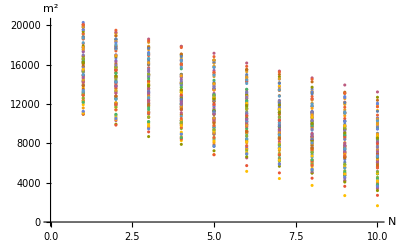

```mathematica
ListPlot[RandomMass,AxesLabel->{Style["N",14],Style["m"^2,14]}]
```

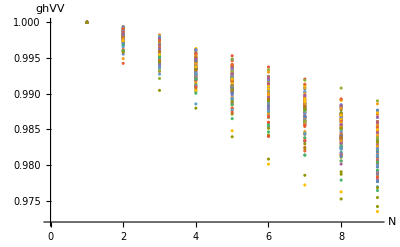

```mathematica
ListPlot[RandomCoupling,AxesLabel->{Style["N",14],Style[ghVV,14]}]
```

## Other way round

Now we study the system on the other way round, we see what is the value of m (the first entry of our mass matrix) that we require in order to have m=125 on the output.

```mathematica
Clear[M,k,m]
```

```mathematica
M=500
k=160
```

500

160

```mathematica
AnalyticMass
```

{{1,List},{2,0.5 (m^2+M^2-1. √(4. k^4+m^4-2. m^2 M^2+M^4))},{3,0.5 (m^2+M^2-1. √(8. k^4+m^4-2. m^2 M^2+M^4))},{4,0.5 (m^2+M^2-1. √(12. k^4+m^4-2. m^2 M^2+M^4))},{5,0.5 (m^2+M^2-1. √(16. k^4+m^4-2. m^2 M^2+M^4))},{6,0.5 (m^2+M^2-1. √(20. k^4+m^4-2. m^2 M^2+M^4))},{7,0.5 (m^2+M^2-1. √(24. k^4+m^4-2. m^2 M^2+M^4))},{8,0.5 (m^2+M^2-1. √(28. k^4+m^4-2. m^2 M^2+M^4))},{9,0.5 (m^2+M^2-1. √(32. k^4+m^4-2. m^2 M^2+M^4))},{10,0.5 (m^2+M^2-1. √(36. k^4+m^4-2. m^2 M^2+M^4))}}

```mathematica
Solve[0.5 (m^2+M^2-1. Sqrt[4(N-1) k^4+m^4-2. m^2 M^2+M^4])==mf^2,m]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{m→-(1. √(-1. k^4+1. M^2 mf^2-1. mf^4+1. k^4 N))/(√(1. M^2-1. mf^2))},{m→(√(-1. k^4+1. M^2 mf^2-1. mf^4+1. k^4 N))/(√(1. M^2-1. mf^2))}}

```mathematica
mInitial[j_,N_]:=Sqrt[-1. k^4+1. M^2 j^2-1. j^4+1. k^4 N]/Sqrt[1. M^2-1. j^2]
```

```mathematica
mInitialvsN1={};
mInitialvsN2={};
mInitialvsN3={};
mInitialvsN4={};
For[i=2,i<n+1,i++,
k=50;
AppendTo[mInitialvsN1,{i,mInitial[125,i]}];
k=90;
AppendTo[mInitialvsN2,{i,mInitial[125,i]}];
k=120;
AppendTo[mInitialvsN3,{i,mInitial[125,i]}];
k=160;
AppendTo[mInitialvsN4,{i,mInitial[125,i]}];
]
```

```mathematica
ListPlot[{mInitialvsN1,mInitialvsN2,mInitialvsN3,mInitialvsN4},PlotLegends->Placed[{"k=50","k=90","k=120","k=160"},{1.2,0.5}],PlotLabel->Style["m_output=125 M=500",16],AxesLabel->{Style["N",14],Style["m (Gev)",14]}]
```

-Graphics-